```mathematica
2-2
```

# Physicist's Introduction to Mathematica 7

## Fourth Edition 2009

## PHYSICS 200

Nicholas Wheeler

REED COLLEGE

## Laboratory 5

## Partial Differential Equations

When you ask Mathematica to solve an ordinary DE—say

```mathematica
(1-x^2)y''[x]-x y'[x]+n^2 y[x]==0
```

or

```mathematica
x''[t]+b x'[t]+ω^2 x[t]==DiracDelta[t]
```

—it has powerful resources to draw upon (the "Kovacic algorithm," "Bocharov techniques," etc.…with altogether use about 300 pages of Mathematica code and 200 pages of C code, we are told), and often has immediate things to say:

```mathematica
DSolve[(1-x^2)y''[x]-x y'[x]+n^2 y[x]==0,y[x],x]
DSolve[x''[t]+b x'[t]+ω^2 x[t]==DiracDelta[t],x[t],t]
```

{{y[x]→C[1] Cosh[n (Log[2]+Log[x+√(-1+x^2)])]+ⅈ C[2] Sinh[n (Log[2]+Log[x+√(-1+x^2)])]}}

{{x[t]→ⅇ^(1/2 t (-b-√(b^2-4 ω^2))) C[1]+ⅇ^(1/2 t (-b+√(b^2-4 ω^2))) C[2]-((ⅇ^(1/2 t (-b-√(b^2-4 ω^2)))-ⅇ^(1/2 t (-b+√(b^2-4 ω^2)))) HeavisideTheta[t])/(√(b^2-4 ω^2))}}

And when those techniques fail one can proceed numerically, with NDSolve, as we have had occasion to  see.

Partial differential equations (PDEs) are, however, a different story. Though

```mathematica
?DSolve
```

DSolve[eqn,y,x] solves a differential equation for the function y, with independent variable x. 
DSolve[{eqn_1,eqn_2,…},{y_1,y_2,…},x] solves a list of differential equations. 
DSolve[eqn,y,{x_1,x_2,…}] solves a partial differential equation.

does speak of PDEs, and Mathematica is by no means powerless in this area (follow the » and go to Scope > Partial Differential Equations), it often responds unhelpfully. Look, for example, to the physically important one-dimensional heat equation (diffusion equation)

```mathematica
D[u[x,t], t]==a D[u[x,t], x,x]
```

concerning which we are told nothing at all:

```mathematica
DSolve[D[u[x,t], t]==a D[u[x,t], x,x],u[x,t],{x,t}]
```

DSolve[u^(0,1)[x,t]==a u^(2,0)[x,t],u[x,t],{x,t}]

It has been my experience that if I—confronted with a PDE—have a plan of attack, then Mathematica will assist me in management of the details.  But Mathematica will not usually devise or even suggest a plan of attack; for those I must read books. PDE's are not nearly so "cut and dried" as ODEs. Let us look to an illustrative instance:

### Waves on a String

#### Form of the General Solution

The one dimensional wave equation reads

```mathematica
c^2 D[u[x,t], x,x]-D[u[x,t], t,t]==0
```

where c is a constant characteristic of the string: it has the physical dimensions of a "velocity," and should not be confused with the "velocity of light." Proceeding

```mathematica
DSolve[c^2 D[u[x,t], x,x]-D[u[x,t], t,t]==0,u[x,t],{x,t}]
```

{{u[x,t]→C[1][t-(√(c^2) x)/c^2]+C[2][t+(√(c^2) x)/c^2]}}

Mathematica informs us—this being the purport of its use of free-floating square brackets (with no function name attached)—that we obtain a solution when we write

```mathematica
u[x,t]:=F[t+x/c]+G[t-x/c] (*Any F[], any G[]*)
```

You had occasion already in 1st-year physics to review the elementary argument that leads to this powerful conclusion, but check it out:

```mathematica
c^2 D[u[x,t], x,x]-D[u[x,t], t,t]==0
```

-F''[t+x/c]-G''[t-x/c]+c^2 (F''[t+x/c]/c^2+G''[t-x/c]/c^2)==0

```mathematica
Simplify[%]
```

True

```mathematica
Clear[u]
```

#### Accommodating Prescribed Initial Conditions: d'Alembert's Formula

Suppose we sought a solution that conforms to prescribed initial conditions:

```mathematica
u[x,0]=f[x] (*any f[]*)
D[u[x,0], t]=g[x] (*any g[]*)
```

The command

```mathematica
Clear[f,g,u]
```

```mathematica
DSolve[{c^2 D[u[x,t], x,x]-D[u[x,t], t,t]==0,
u[x,0]==f[x],
D[u[x,t], t]==g[x]},u[x,t],{x,t}]
```

DSolve[{-u^(0,2)[x,t]+c^2 u^(2,0)[x,t]==0,u[x,0]==f[x],u^(0,1)[x,t]==g[x]},u[x,t],{x,t}]

got us nowhere.  Yet we learn from books that an elegant solution of that initial value problem was known already (by about 1750) to  (who initiated the study of strings, and thus of PDEs):

```mathematica
u[x,t]=1/2(f[x+c t]+f[x-c t])+1/(2c)∫_(x-c t)^(x+c t) g[ξ]ⅆξ
```

1/2 (f[-c t+x]+f[c t+x])+(∫_(-c t+x)^(c t+x) g[ξ]ⅆξ)/(2 c)

And Mathematica, once pointed in the right direction, is quick to agree with d'Alembert: the function to which d'Alembert's formula leads does satisfy the wave equation

```mathematica
c^2 D[u[x,t], x,x]-D[u[x,t], t,t]==0//Simplify
```

True

and does conform to the prescribed initial conditions:

```mathematica
u[x,t]/.t->0
D[u[x,t], t]/.t->0
```

f[x]

g[x]

It is when we decide to use these results to explore particular cases that Mathematica comes again most vividly into its own:

```mathematica
Clear[u]
```

#### First Example

```mathematica
u[x,t]:=Sin[t-x/c]
```

```mathematica
c^2 D[u[x,t], x,x]-D[u[x,t], t,t]==0
```

True

If we wanted to display that result on the printed page we might assign c a convenient value (I set c = 1) and proceed

```mathematica
c=1
```

1

```mathematica
Plot3D[Sin[t-x],{x,-2π,2π},{t,0,6},PlotPoints->30,
AxesLabel->{"position x","time t","amplitude"},
Ticks->{None, Automatic, None}]
```

-Graphics3D-

NOTE: On the Mathematica 7 screen we are not stuck with a single view of that surface, as we would be in a book.

But if we planned to speak about it in a modern lecture hall we would probably find it more effective to use one means or another to animate the figure: Mathematica 6 permits us to proceed

```mathematica
Manipulate[Plot[Sin[t-x],{x,-2π,2π}],{t,0,4π}]
```

INSTRUCTION: Hit the + button to expose the controls, then hit the "play" button.

or, alternatively,

```mathematica
Animate[Plot[Sin[t-x],{x,-2π,2π}],{t,0,4π},AnimationRunning->False]
```

```mathematica
Clear[u]
```

#### Second Example

```mathematica
u[x,t]:=Sin[t-x/c]+1/3 Cos[3(t+x/c)]
```

```mathematica
c^2 D[u[x,t], x,x]-D[u[x,t], t,t]==0//Simplify
```

True

```mathematica
φ[x,t]:=u[x,t]/.c->1
```

```mathematica
φ[x,t]
```

1/3 Cos[3 (t+x)]+Sin[t-x]

The static 3D figure is now almost too complicated to be informative:

```mathematica
Plot3D[1/3 Cos[3 (t+x)]+Sin[t-x],{x,-2π,2π},{t,0,6},PlotPoints->30,
AxesLabel->{"position x","time t","amplitude"},
Ticks->{None, Automatic, None}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[{1/3 Cos[3 (t+x)],Sin[t-x],1/3 Cos[3 (t+x)]+Sin[t-x]},{x,-2π,2π},PlotStyle->{{Blue,Thickness[.004]},{Green,Thickness[.004]},{Red,Thickness[.01]}},PlotRange->{-1.5,1.5}],{t,0,4π,N[π/20]}]
```

INSTRUCTIONS: Hit the + button to expose the controls, then hit the "play" button. Slow down the motion to see more clearly that the blue sine curve slides rigidly to the left, while the  green sine curve slides rigidly to the right (at the same speed),

```mathematica
Clear[u]
```

#### Third Example: d'Alembert's Solution

d'Alembert speaks of the wave form that evolves from prescribed initial data (a "thrown wave," if you will—the term borrowed from what we prescribe when we throw a rock).

Let us suppose, first off, that the string is intially at rest, but has a Gaussian profile:

```mathematica
f[x]:=ⅇ^(-x^2/4)
g[x]:=0
```

d'Alembert's formula then supplies

```mathematica
u[x,t]=1/2(f[x+c t]+f[x-c t])+1/(2c)∫_(x-c t)^(x+c t) g[ξ]ⅆξ
```

then supplies

```mathematica
u1[x_,t_]:=1/2(ⅇ^(-(x+t)^2/4)+ⅇ^(-(x-t)^2/4))
```

```mathematica
D[u1[x,t], x,x]-D[u1[x,t], t,t]==0//Simplify
```

True

```mathematica
Manipulate[Plot[u1[x,t],{x,-20,20},PlotRange->{0,1},Ticks->{{-20,-10,10,20},{0.5,1.0}}],{t,0,20}]
```

When the initially static Gaussian is released it resolves into two half-sized Gaussians traveling in opposite directions.

Going now to the other extreme, let us suppose that the string is initially flat, but that it has been given a Gaussian velocity profile, centered at the origin (where it has been "plucked"). Recall that the Gaussian (or "normal") distribution function is defined

```mathematica
g[x_,a_]:=1/(a √π)ⅇ^(-(x/a)^2)
```

and responds to manipulation of the a-parameter as shown below:

```mathematica
Manipulate[Plot[g[x,a],{x,-20,20},PlotRange->{0,1}],{a,.5,5}]
```

The area under each of those curves is unity.

To model a "central pluck" we set a = 1 (use the figure to see that the Gaussian is then fairly narrow/compactly localized) and—from d'Alembert's formula

```mathematica
u[x,t]=1/2(f[x+c t]+f[x-c t])+1/(2c)∫_(x-c t)^(x+c t) g[ξ]ⅆξ
```

by evaluation  of the intergral

```mathematica
1/2∫_(x- t)^(x+ t) g[ξ,1]ⅆξ
```

1/4 (Erf[t-x]+Erf[t+x])

—obtain

```mathematica
u2[x_,t_]:=1/4 (Erf[t-x]+Erf[t+x])
```

REMARK: By now you probably don't need to be reminded that the following command

```mathematica
?Erf
```

Erf[z] gives the error function erf(z). 
Erf[z_0,z_1] gives the generalized error function erf(z_1)-erf(z_0).

will lead you to a source of information abou the error function Erf[x].

```mathematica
Manipulate[Plot[u2[x,t],{x,-20,20},PlotRange->{0,1},Ticks->{{-20,-10,10,20},{0.5,1.0}}],{t,0,20}]
```

INSTRUCTIONS: The opening scenes are best viewed if one manipulates the slide control by hand.

The string is seen to respond to having been "plucked" by developing a central deformation (the shape of which looks pretty Gaussian) which, after achieving its full size, spreads like a contagion to left and right. It may, on first blush, seem surprising that the pulse spreads without attenuation. This is a consequence of the one-dimensionality of strings. In N-dimensions, effects that "fall off geometrically" fall off as 1/r^(N-1), so on strings they fall off as  1/r^0, which is to say: not at all. In the present instance, the "effect" in question might be taken to be energy flux, which can be shown by physical argument to be proportional to (∂_t u[x,t])^2 and is non-zero only at the leading/trailing edges of the waveform, as shown in the following figure:

```mathematica
D[u2[x,t],t]^2
```

1/16 ((2 ⅇ^(-(t-x)^2))/(√π)+(2 ⅇ^(-(t+x)^2))/(√π))^2

```mathematica
Manipulate[Plot[1/16 ((2 ⅇ^(-(t-x)^2))/(√π)+(2 ⅇ^(-(t+x)^2))/(√π))^2,{x,-20,20},PlotRange->{0,1},Ticks->{{-20,-10,10,20},{0.5,1.0}}],{t,0,20}]
```

The  energy invested by the "pluck" is seen to two localized packets, that propagate left and right.

### Accommodating Prescribed Boundary Conditions: the Clamped String

Suppose we "clamp" the string at  x=0. We are led then to look among general solutions of the wave equation

```mathematica
u[x_,t_]:=F[t+x/c]+G[t-x/c]
```

for solutions with the property that

```mathematica
u[0,t]=0   :   all t
```

From

```mathematica
u[0,t]
```

F[t]+G[t]

we conclude that u[x, t] must have the specialized form

```mathematica
Clear[u]
```

```mathematica
u[x_,t_]:=F[t+x/c]-F[t-x/c]
```

```mathematica
u[x,t]
```

-F[t-x]+F[t+x]

Suppose, now, that we install a second clamp at x=a:

```mathematica
u[a,t]=0   :   all t
```

From

```mathematica
u[a,t]
```

-F[-a+t]+F[a+t]

we conclude that F[] must have the property that

```mathematica
F[t]=F[t+2 a/c]   :   all t
```

i.e., that F[] must be periodic:

```mathematica
F[t]=F[t+n(2a)/c]   :   n=0,±1,±2,...  ;  all t
```

#### Simple Example

Let F[] be the simplest of functions with the required period:

```mathematica
F[ξ]=Sin[2π c/(2a)ξ]
```

Then

```mathematica
u[x,t]=Sin[2π c/(2a)(t+x/c)]-Sin[2π c/(2a)(t-x/c)]
```

But

```mathematica
Sin[2π c/(2a)(t+x/c)]-Sin[2π c/(2a)(t-x/c)]//Simplify
```

2 Cos[(π t)/a] Sin[(π x)/a]

so we have

```mathematica
u[x,t]=2 Cos[2π(c t)/(2a)] Sin[2π x/(2a)]
```

2 Cos[(π t)/a] Sin[(π x)/a]

which describe a standing wave, with

period τ = 2a/c
frequency f=1/τ=c/2a
wavelength = 2a

frequency * wavelength = c

Setting a = c = 1, we have this representation of the situation

```mathematica
Manipulate[Plot[2 Cos[π t] Sin[π x],{x,0,1}, PlotRange->{-2,2}, Ticks->{0,1},{}],{t,0,2}]
```

INSTRUCTIONS: Hit the + button, then run the animation.

The next figure shows how counter-running sine waves conspire to produce a standing wave:

```mathematica
Manipulate[Plot[{Sin[π (t+x)],-Sin[π (t-x)],Sin[π (t+x)]-Sin[π (t-x)]},{x,-3,4},PlotStyle->{{Blue,Thickness[.004]},{Green,Thickness[.004]},{Red,Thickness[.01]}},PlotRange->{-4,4}, Ticks->{{0,1},{}}],{t,0,4π,N[π/30]}]
```

INSTRUCTIONS: Hit the + button, then run the animation but be sure to slow it way down. The physical  part of the display is confined to the interval 0 ⩽ x ⩽ 1.

The following figure shows only the "physical part" of the solution. Note that the ends of the red curve are in fact "clamped," and notice how that comes about.

```mathematica
Manipulate[Plot[{Sin[π (t+x)],-Sin[π (t-x)],Sin[π (t+x)]-Sin[π (t-x)]},{x,0,1},PlotStyle->{{Blue,Thickness[.004]},{Green,Thickness[.004]},{Red,Thickness[.01]}},PlotRange->{-4,4}, Ticks->{{0,1},{}}],{t,0,4π,N[π/30]}]
```

#### Effect of Releasing a Clamp

At the unclamped ends of a string it is—for physical reasons, arising from the that energy/momentum must vanish at such points—not the value but the spatial derivative of the field function that must vanish. This serves, in effect, to double the allowed  wave lengths, and halve the allowed frequencies. The following animation shows a string that is vibrating with both ends clamped when suddenly the clamp on the right is released.  Note the kink that then ripples back and forth along the string,

```mathematica
ϕ[x_,t_]:=1/2(Cos[π t]+Sin[π t])Sin[π x]
Φ[x_,t_,f1_,g1_,p_]:=∑_(k=0)^p (f1 8/((4-(2k+1)^2)π)Sin[((2k+1)π)/2]Cos[(2k+1)/2 π t]+
g1 2/(2k+1)8/((4-(2k+1)^2)π)Sin[((2k+1)π)/2]Sin[(2k+1)/2 π t])Sin[((2k+1)π)/2 x]
```

We  use the UnitStep function to switch off the clamped/clamped solution and to switch on the clamped/unclamped solution at time t > 0:

```mathematica
string[x_,t_]:=ϕ[x,t](1-UnitStep[t])+Φ[x,t,1/2,1/2,15]UnitStep[t]
```

We ask Mathematica to construct an animated illustration of the resulting string motion:

```mathematica
Animate[Plot[string[x,t],{x,0,1}, PlotRange->{-1.5,1.5}, Ticks->{{1},{-1,1}}],{t,-2.25,4,0.01},AnimationRate->.2,AnimationRunning->False]
```

Note the kink that then ripples back and forth along the string. Note particularly that it reverses sign when reflected from the clamped end, but preserves its sign  when reflected  from the unclamped end of the string. The problem is made interesting by the fact that it involves abrupt change of a boundary condition. For the source of my interest in the problem, see discussion on the web of the famous . Look particularly at the final videos.

#### Another Interesting Example: Gaussian Pulse on a Clamped String

From any f[ξ] that is well-defined for all ξ, construct

```mathematica
F[ξ]=∑_(n =-∞)^∞ f[ξ+n p]
```

and assume the infinite sum to be convergent. Clearly, every such F[ξ] will be periodic:

```mathematica
F[ξ]=F[ξ+n p]   :   n=0,±1,±2,...
```

Suppose, in particular, that we use the previously-encountered Gaussian function

```mathematica
g[ξ_,a_]:=1/(a √π)ⅇ^(-(ξ/a)^2)
```

go define

```mathematica
f[ξ_]:=(√π)/15 g[ξ-1/2,1/15]
```

and then to construct (NOTE the necessarily truncated sum)

```mathematica
F[ξ_]:=∑_(n=-5)^5 f[ξ+2n]
```

The following figure shows that we have successfully constructed a functions that has (at least in the neighborhood of interest) period p = 2  :

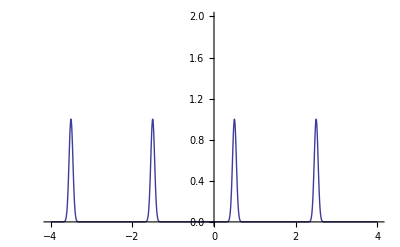

```mathematica
Plot[F[ξ],{ξ,-4,4},PlotRange->{0,2}]
```

```mathematica
Manipulate[Plot[F[t+x]-F[t-x], {x,0,1},PlotRange->{-2,2}, Ticks->{{0,1},{}},PlotStyle->{Red,Thickness[.01]}],{t,0,2,0.02}]
```

INSTRUCTIONS: Animation tends in this instance to miss details at the times when the pulse is bouncing off one or the other of the clamps. Hand operation of the slider provides better control.

### Solution by "Separation of Variables"

Our discussion of standing waves culmiated in a wave function of the form

u[x,t]=2 Cos[2π t/τ] Sin[2π x/λ]

in which the variables x and t have been "separated," in the sense that they appear as the arguments of distinct and separate functions, which are multiplied together. Had we specifically sought  wave functions with that separated structure, the problem of solving the wave equation would have assumed quite a different aspect, as I now demonstrate:

```mathematica
Clear[u,f,g]
```

Assume the wave function to be a product function:

```mathematica
u=f[x]*g[t]
```

f[x] g[t]

From

```mathematica
(c^2 D[u, x,x]-D[u, t,t])/u//Simplify
```

f''[x]/f[x]-g''[t]/g[t]

we learn that the wave equation can be written

```mathematica
(c^2 f''[x])/f[x]-g''[t]/g[t]=0
```

But this requires that (c^2 f''[x])/f[x]and g''[t]/g[t] be separately equal to some mutual "separation constant":

```mathematica
(c^2 f''[x])/f[x]=k
g''[t]/g[t]=k
```

From

```mathematica
DSolve[g''[t]/g[t]==k,g[t],t]
```

{{g[t]→ⅇ^(√k t) C[1]+ⅇ^(-√k t) C[2]}}

we learn that, if we are to avoid exponential inflation/death the separation constant must be negative, which we emphasize by writing

```mathematica
k=-ω^2
```

The command

```mathematica
DSolve[g''[t]/g[t]==-ω^2,g[t],t]
```

{{g[t]→C[1] Cos[t ω]+C[2] Sin[t ω]}}

yields an oscillatory function, with period τ = 2 π/ω. The command

```mathematica
DSolve[(c^2 f''[x])/f[x]==-ω^2,f[x],x]
```

{{f[x]→C[1] Cos[x ω]+C[2] Sin[x ω]}}

yields functions that are spatially oscillatory, with wavelength

```mathematica
λ=2π c/ω
```

(2 π)/ω

To achieve clamping at x=0 and x=a we are obliged to set

```mathematica
C[1]=0
a ω/c=n π   :   n=0,1,2,...
```

The latter equation can be formulated

```mathematica
Subscript[λ, n]=(2a)/n
```

Boundary conditions have forced the abandonment of all but a discrete set of wavelengths, and therefore all but a discrete set (spectrum) of frequencies

```mathematica
Subscript[f, n]=Subscript[ω, n]/2π =(c/2a)n=c/Subscript[λ, n]
```

It is in connection with higher-dimensional problems that the Method of Separation of Variables most vividly reveals its exceptional power.  Note in this connection that

• in 2D boundaries become curves;

• in 3D boundaries become surfaces.

I illustrate the method as it pertains to the…

#### Vibration of a Circular Drumhead

We want to solve

```mathematica
c^2(D[u[x,y,t], x,x]+∂_(y,y) u[x,y,t])-D[u[x,y,t], t,t]==0
```

subject to the requirement that u[x, y, t] vanishes (all t) at the boundary of a circle of radius a.

The shape of the boundary makes it natural to work in polar coordinates:

```mathematica
x=r Cos[θ]
y=r Sin[θ]
```

We write

```mathematica
u[x,y]=F[r[x,y],θ[x,y]]
```

with

```mathematica
r[x_,y_]:=√(x^2+y^2)
θ[x_,y_]:=ArcTan[x,y]
```

In this notation ∂_(x,x) u[x,y,t]+∂_(y,y) u[x,y,t]becomes

```mathematica
D[F[r[x,y],θ[x,y]],{x,2}]+
D[F[r[x,y],θ[x,y]],{y,2}]
```

-(x^2 F^(1,0)[√(x^2+y^2),ArcTan[x,y]])/((x^2+y^2)^(3/2))-(y^2 F^(1,0)[√(x^2+y^2),ArcTan[x,y]])/((x^2+y^2)^(3/2))+(2 F^(1,0)[√(x^2+y^2),ArcTan[x,y]])/(√(x^2+y^2))-(y (-(y F^(0,2)[√(x^2+y^2),ArcTan[x,y]])/(x^2+y^2)+(x F^(1,1)[√(x^2+y^2),ArcTan[x,y]])/(√(x^2+y^2))))/(x^2+y^2)+(x ((x F^(0,2)[√(x^2+y^2),ArcTan[x,y]])/(x^2+y^2)+(y F^(1,1)[√(x^2+y^2),ArcTan[x,y]])/(√(x^2+y^2))))/(x^2+y^2)+(x (-(y F^(1,1)[√(x^2+y^2),ArcTan[x,y]])/(x^2+y^2)+(x F^(2,0)[√(x^2+y^2),ArcTan[x,y]])/(√(x^2+y^2))))/(√(x^2+y^2))+(y ((x F^(1,1)[√(x^2+y^2),ArcTan[x,y]])/(x^2+y^2)+(y F^(2,0)[√(x^2+y^2),ArcTan[x,y]])/(√(x^2+y^2))))/(√(x^2+y^2))

```mathematica
Simplify[%]
```

1/((x^2+y^2)^(3/2))(√(x^2+y^2) F^(0,2)[√(x^2+y^2),ArcTan[x,y]]+(x^2+y^2) (F^(1,0)[√(x^2+y^2),ArcTan[x,y]]+√(x^2+y^2) F^(2,0)[√(x^2+y^2),ArcTan[x,y]]))

```mathematica
%/.{√(x^2+y^2)->r,ArcTan[x,y]->θ}
```

(r F^(0,2)[r,θ]+(x^2+y^2) (F^(1,0)[r,θ]+r F^(2,0)[r,θ]))/((x^2+y^2)^(3/2))

```mathematica
%/.{(x^2+y^2)->r^2}
```

(r F^(0,2)[r,θ]+r^2 (F^(1,0)[r,θ]+r F^(2,0)[r,θ]))/((r^2)^(3/2))

Mathematica does not know what to do with the (r^2)^(3/2)because it does not know whether r is positive or negative. So we tell it:

```mathematica
Simplify[%, r>0]
```

(F^(0,2)[r,θ]+r (F^(1,0)[r,θ]+r F^(2,0)[r,θ]))/r^2

In polar coordinates, our problem, therefore, is to solve

```mathematica
c^2(D[F[r,θ,t], r,r]+1/r D[F[r,θ,t], r]+1/r^2 D[F[r,θ,t], θ,θ])-D[F[r,θ,t], t,t]=0
```

subject to the requirement that

```mathematica
F[a,θ,t]=0   :  all θ, all t
```

To that end, we make the characteristic "separation assumption" that

```mathematica
F[r,θ,t]=R[r]*S[θ]*T[t]
```

R[r] S[θ] T[t]

We command

```mathematica
(c^2(D[F[r,θ,t], r,r]+1/r D[F[r,θ,t], r]+1/r^2 D[F[r,θ,t], θ,θ])-D[F[r,θ,t], t,t])/F[r,θ,t]//Simplify
```

(R'[r]/r+R''[r])/R[r]+S''[θ]/(r^2 S[θ])-T''[t]/T[t]

and conclude that the following (decoupled)  statements must hold individiually:

```mathematica
T''[t]/T[t]=-ω^2
(c^2 (R'[r]+r R''[r]))/(r R[r])+(c^2 S''[θ])/(r^2 S[θ])=-ω^2
```

#### Evaluating the Secular Factor

Look first to the former:

```mathematica
DSolve[T''[t]/T[t]==-ω^2,T[t],t]
```

{{T[t]→C[1] Cos[t ω]+C[2] Sin[t ω]}}

We conclude that T[t]is harmonic, with angular frequency ω :

```mathematica
T[t_]:=A Sin[ω t+δ]
```

#### Evaluating the Angular Factor

Command

```mathematica
r^2/c^2((c^2 (R'[r]+r R''[r]))/(r R[r])+(c^2 S''[θ])/(r^2 S[θ])+ω^2)//Expand
```

r^2 ω^2+(r R'[r])/R[r]+(r^2 R''[r])/R[r]+S''[θ]/S[θ]

and since this expression must vanish we have the separated equations

```mathematica
S''[θ]/S[θ]=-m^2
(r^2 ω^2)/c^2+(r R'[r])/R[r]+(r^2 R''[r])/R[r]=+m^2
```

The command

```mathematica
DSolve[S''[θ]/S[θ]==-m^2,S[θ],θ]
```

{{S[θ]→C[1] Cos[m θ]+C[2] Sin[m θ]}}

The fact that the wave function (since it refers to the instantaneous shape of the drumhead) must be single-valued, which forces us to insist that

```mathematica
F[r,θ+2π,t]=F[r,θ,t]
```

which forces us to insist that

```mathematica
S[θ+2π]=S[θ]
```

which in turn forces us to set m = 0, 1, 2, ... , giving S[θ]=Sin[m θ+θ_0]. We will find it most convenient to set

```mathematica
S[θ]=Cos[m θ]   :   m=0,1,2,...
```

#### A More Intricate Business: Evaluating the Radial Factor

It remains to consider the equation

r^2 R''[r]+r R'[r]+(k^2 r^2-m^2)R[r]=0   :   k≡ ω/c

We command

```mathematica
DSolve[r^2 R''[r]+r R'[r]+(k^2 r^2-0^2)R[r]==0,R[r],r]
DSolve[r^2 R''[r]+r R'[r]+(k^2 r^2-1^2)R[r]==0,R[r],r]
DSolve[r^2 R''[r]+r R'[r]+(k^2 r^2-2^2)R[r]==0,R[r],r]
DSolve[r^2 R''[r]+r R'[r]+(k^2 r^2-3^2)R[r]==0,R[r],r]
```

{{R[r]→BesselJ[0,k r] C[1]+BesselY[0,k r] C[2]}}

{{R[r]→BesselJ[1,k r] C[1]+BesselY[1,k r] C[2]}}

{{R[r]→BesselJ[2,k r] C[1]+BesselY[2,k r] C[2]}}

{{R[r]→BesselJ[3,k r] C[1]+BesselY[3,k r] C[2]}}

At this point we could command

```mathematica
?BesselJ
```

BesselJ[n,z] gives the Bessel function of the first kind J_n(z).

but will instead proceed graphically:

```mathematica
Manipulate[Plot[BesselJ[m,ρ],{ρ,0,20}, PlotRange->{-.5,1}],{m,0,10,1}]
```

INSTRUCTIONS: Hit the + button to expose the controls, use the ± buttons to show graphs of some low-order Bessel function.

We require that the wave function vanish on the circular boundary of the drumhead

```mathematica
F[a,θ,t]=0
```

so have interest only those k-values for which

```mathematica
BesselJ[m,k a]=0
```

We have interest, that is to say, in the numbers k_(m,n) with the property that

```mathematica
Subscript[k, m,n] a=n^th zero of BesselJ[m,ρ],the Bessel function of  order m
```

NOTE: We have   ω ≡ c k, so from the fact that the set of admissible k-values is discrete it follows that so also is the set of natural frequencies discrete:

```mathematica
Subscript[ω, m,n]=c Subscript[k, m,n]
```

To find the n^th zero of  BesselJ[m, ρ]  we might use the command

```mathematica
?FindRoot
```

FindRoot[f,{x,x_0}] searches for a numerical root of f, starting from the point x=x_0.
FindRoot[lhs==rhs,{x,x_0}] searches for a numerical solution to the equation lhs==rhs. 
FindRoot[{f_1,f_2,…},{{x,x_0},{y,y_0},…}] searches for a simultaneous numerical root of all the f_i.
FindRoot[{eqn_1,eqn_2,…},{{x,x_0},{y,y_0},…}] searches for a numerical solution to the simultaneous equations eqn_i.

…which works like this: From the figure

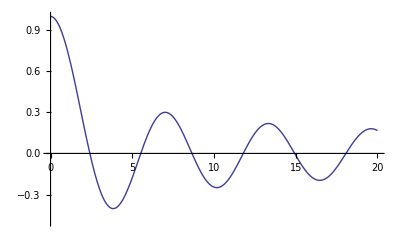

```mathematica
Plot[BesselJ[0,ρ],{ρ,0,20}, PlotRange->{-.5,1}]
```

we see that the leading zero of BesselJ[0, ρ] lies in the neighborhood of ρ = 2.5, so we ask Mathematica to search for a zero in that neighborhood:

```mathematica
FindRoot[BesselJ[0,ρ]==0,{ρ,2.5}]
```

{ρ→2.40483}

To find the next zero we command

```mathematica
FindRoot[BesselJ[0,ρ]==0,{ρ,5.6}]
```

{ρ→5.52008}

and so we might proceed. But Mathematica provides a command

```mathematica
?BesselJZero
```

BesselJZero[n,k] represents the k^th zero of the Bessel function J_n(x).
BesselJZero[n,k,x_0] represents the k^th zero greater than x_0.

that does the work for us:

```mathematica
BesselJZero[0,1]//N
BesselJZero[0,2]//N
```

2.40483

5.52008

The following command creates a table, in which the first row presents the zeros of BesselJ[0, ρ] in ascending order, the second row presents the zeros of BesselJ[1, ρ], etc.

```mathematica
Table[BesselJZero[m,n]//N,{m,0,3},{n,1,5}]//TableForm
```

2.40483 | 5.52008 | 8.65373 | 11.7915 | 14.9309
3.83171 | 7.01559 | 10.1735 | 13.3237 | 16.4706
5.13562 | 8.41724 | 11.6198 | 14.796 | 17.9598
6.38016 | 9.76102 | 13.0152 | 16.2235 | 19.4094

From

```mathematica
Subscript[ω, m,n]=(c/a)BesselJZero[m,n]
```

we become able, by inspection of the table, to list in ascending order the natural frequencies of a vibrating circular drumhead:

```mathematica
Subscript[ω, 0,1]  :   fundamental
Subscript[ω, 1,1]  :   first harmonic
Subscript[ω, 2,1]  :   second harmonic
Subscript[ω, 0,2]  :   third harmonic
Subscript[ω, 3,1]  :   fourth harmonic
⋮
```

#### Assembly of the Final Result

We have now in hand this doubly-indexed population of solutions of the equation of motion of a circular drumhead:

```mathematica
F[r_,θ_,t_,m_,n_,c_,a_]:=BesselJ[m,N[BesselJZero[m,n]]/a r]*Cos[m θ]*Cos[(c/a)N[BesselJZero[m,n]]t]
```

The radial factors

```mathematica
R[r_,m_,n_,a_]:=BesselJ[m,N[BesselJZero[m,n]]/a r]
```

of low order—displayed as functions of ρ = r/a (which ranges between 0 and 1)—look like this:

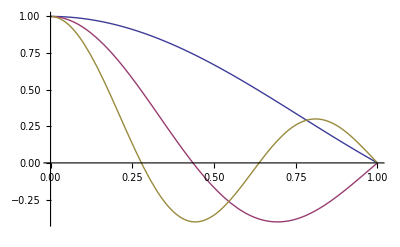

```mathematica
Plot[Evaluate[{R[ρ,0,1,1],R[ρ,0,2,1],R[ρ,0,3,1]}],{ρ,0,1}]
```

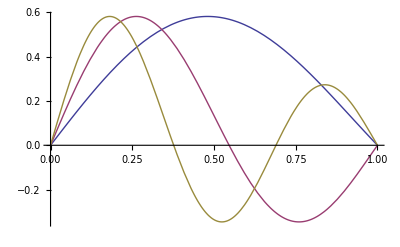

```mathematica
Plot[Evaluate[{R[ρ,1,1,1],R[ρ,1,2,1],R[ρ,1,3,1]}],{ρ,0,1}]
```

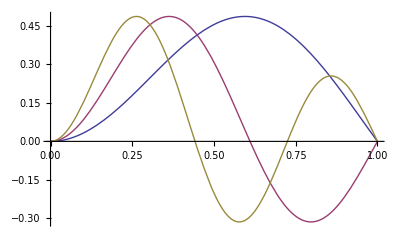

```mathematica
Plot[Evaluate[{R[ρ,2,1,1],R[ρ,2,2,1],R[ρ,2,3,1]}],{ρ,0,1}]
```

When we undertake to construct animated displays of various modes of drumhead vibration we discover

```mathematica
?PolarPlot3D
```

Information::notfound: Symbol PolarPlot3D not found.

that Mathematica 7 does not provide a PolarPlot3D command, so are forced to work in Cartesian coordinates:

```mathematica
Clear[u]
```

```mathematica
u[x_,y_,t_,m_,n_,c_,a_]:=F[√(x^2+y^2),ArcTan[x,y],t,m,n,c,a]
```

REMARK: From

```mathematica
?ArcTan
```

ArcTan[z] gives the arc tangent tan^-1(z) of the complex number z. 
ArcTan[x,y] gives the arc tangent of y/x, taking into account which quadrant the point (x,y) is in.

we learn that Mathematica recognizes two distinct ArcTan commands. It is to avoid catastrophy in  the construction of some subsequent figures that we have adopted the second alternative.

We look now to animated graphic representations of the following low-order vibrational modes:

```mathematica
fundamental[x_,y_,t_]:=u[x,y,t,0,1,1,1]
firstharmonic[x_,y_,t_]:=u[x,y,t,1,1,1,1]
secondharmonic[x_,y_,t_]:=u[x,y,t,2,1,1,1]
thirdharmonic[x_,y_,t_]:=u[x,y,t,0,2,1,1]
fourthharmonic[x_,y_,t_]:=u[x,y,t,3,1,1,1]
higherharmonic[x_,y_,t_]:=u[x,y,t,5,2,1,1]
```

REMARK: When viewing the following animations—which are activated in the familiar way—one must mentally trim off and discard the part of the membrane that lies outside the unit circle. It is sometimes easier to see what is going on if (with the animation stopped) one adjusts the viewpoint.

QUIRK: Sometimes, after construction of the figure is complete, the cell marker on the right looks like Mathematica is still thinking. Scroll, and that misleading indicator will disappear. This should be done before you make your next command.

```mathematica
Manipulate[Plot3D[Evaluate[fundamental[x,y,t]],{x,-1,1},{y,-1,1},PlotRange->{-1,1},Ticks->{{-1,1},{-1,1},{0}}],{t,0,(2π)/BesselJZero[0,1]}]
```

```mathematica
Manipulate[Plot3D[Evaluate[firstharmonic[x,y,t]],{x,-1,1},{y,-1,1},PlotRange->{-1,1},Ticks->{{-1,1},{-1,1},{0}}],{t,0,(2π)/BesselJZero[1,1]}]
```

```mathematica
Manipulate[Plot3D[Evaluate[secondharmonic[x,y,t]],{x,-1,1},{y,-1,1},PlotRange->{-1,1},Ticks->{{-1,1},{-1,1},{0}}],{t,0,(2π)/BesselJZero[2,1]}]
```

```mathematica
Manipulate[Plot3D[Evaluate[thirdharmonic[x,y,t]],{x,-1,1},{y,-1,1},PlotRange->{-1,1},Ticks->{{-1,1},{-1,1},{0}}],{t,0,(2π)/BesselJZero[0,2]}]
```

```mathematica
Manipulate[Plot3D[Evaluate[fourthharmonic[x,y,t]],{x,-1,1},{y,-1,1},PlotRange->{-1,1},Ticks->{{-1,1},{-1,1},{0}}],{t,0,(2π)/BesselJZero[3,1]}]
```

```mathematica
Manipulate[Plot3D[Evaluate[higherharmonic[x,y,t]],{x,-1,1},{y,-1,1},PlotRange->{-1,1},Ticks->{{-1,1},{-1,1},{0}}],{t,0,(2π)/BesselJZero[5,2]}]
```

NOTICE that is is only in the animations of the fundamental and 3rd harmonic that the center of the drumhead moves: in all other cases it is static. This is because

BesselJ[m,0]=0   unless   m=0

All modes that display center motion are axially symmetric, as is evident in the following figure:

```mathematica
Manipulate[Plot3D[Evaluate[u[x,y,t,0,5,1,1]],{x,-1,1},{y,-1,1},PlotRange->{-1,1},Ticks->{{-1,1},{-1,1},{0}}],{t,0,(2π)/BesselJZero[0,5]}]
```

### Summary Remarks Concerning the Separation Method

The following remarks are of general significance, but will be phrased as they relate to our experience with the drum problem:

• Separation proceeded from a strong factorization assumption

```mathematica
u[r,θ,t]=R[r]*A[θ]*f[t]
```

and led to particular solutions of the PDE in question.  But the general solution (it could be shown) can be developed as a linear combination (superposition) of those particular solutions.

• Spectral discreteness arose not from the PDE itself (which speaks in the language of smooth variation) but from the associated boundary conditions. It is from this same circumstance that quantum mechanics acquires the quantal discreteness to which its name refers, and so does music.

• Mathematica made duck soup of the computational/graphic details, but we ourselves were responsible for the controlling ideas—responsible, in particular, for the decision to work in polar coordinates.

• The decision to work in polar coordinates served us in two distinct ways: (1) it permitted separation of the PDE, and (2) it permitted natural description of the boundary conditions.  The theory in hand could be adapted to a theory of wedge-shaped drumheads (more generally: any drumheads bounded by arcs of constant r and arcs of constant θ), but it has nothing to say about (say) elliptical drums, or annular drumheads with off-center holes.

• All strings have the same shape, and support therefore similar sets of harmonics. But drumheads (2-dimensional systems) can have an infinite variety of shapes, and each supports its own distinct  set of harmonics. It becomes plausibe to speculate that one can "hear the shape of a drum."

• Our ability to adapt the separation of variables method to other physical problems is limited by our command of separating coordinate systems, and we can expect in all events to be able to deal only with systems in which the boundaries conform to the geometry of whatever coordinate system we have selected. (In other—more general cases—we would have to fall back on numerical methods which are a vast subject in themselves.)

The latter circumstance has—more than any other—inspired development of a great number of wonderful coordinate systems, about which Mathematica knows a great deal. Moreover, variable-separation procedures, carried out in those diverse coordinate systems, have inspired the invention and study of many of the "higher transcendental functions" (things like the Bessel functions encountered above) that are the bread & butter of mathematical physics, and about which Mathematica also knows a great deal.

## Curvilinear Coordinate Systems

### To and From Various Coordinate Systems

To activate Mathematica's expert command of this subject one must enter the Vector Analysis Package. For a survey of that resource, go to Help > Documentation Center and search for VectorAnalysis/guide/VectorAnalysisPackage. There you will be directed (see TUTORIALS at the bottom of the page) to the very informative VectorAnalysis/tutorial/VectorAnalysis. To import the package, command

```mathematica
Needs["VectorAnalysis`"]
```

The command

```mathematica
CoordinateSystem
```

Cartesian

identifies the default coordinate system. The commands

```mathematica
SetCoordinates[Cartesian]
SetCoordinates[Spherical]
SetCoordinates[Polar]
```

Cartesian[Xx,Yy,Zz]

Spherical[Rr,Ttheta,Pphi]

Coordinates::invalid: Polar is not a valid coordinate system specification.

SetCoordinates[Polar]

inform us that—until instructed otherwise—Mathematica will assume Cartesian coodinates to be named {x,y,z} (or perhaps {X,Y,Z}), spherical coordinates to be named {r, theta, phi} (or perhaps {R, T, P}), and that polar coordinates fall outside the perview of the package, which has things to say only about 3-dimensional coordinate systems. These are the names of the coordinate ystems it is prepared to discuss:

• Bipolar

• Cartesian

• ConfocalParaboloidal

• Cylindrical

• OblateSpheroidal

• Paraboloidal

• Spherical

• Bispherical

• ConfocalEllipsoidal

• Conical

• EllipticCylindrical

• ParabolicCylindrical

• ProlateSpereoidal

• Toroidal

And Mathematica stands ready to tell us what it means by each. Let us look, for example, to the Spherical coordinate system:

```mathematica
SetCoordinates[Spherical]
```

Spherical[Rr,Ttheta,Pphi]

```mathematica
CoordinatesToCartesian[{r,θ,ϕ},Spherical]
```

{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ]}

This means that Mathematica has defined

```mathematica
x[r_,θ_, ϕ_]:=r Sin[θ]Cos[ϕ]
y[r_,θ_, ϕ_]:=r Sin[θ]Sin[ϕ]
z[r_,θ_, ϕ_]:=r Cos[θ]
```

and so interprets θ to be not latitude but "co-latitude": θ is 0 at the north pole, π at the south pole (not 0 at the equator, as  geographers and some physicists/mathematicians assume). This is, in particular, the spherical system employed by Griffiths in his Introduction to Electrodynamics (see the endpapers). To clarify the situation, we have the command

```mathematica
CoordinateRanges[Spherical]
```

{0≤Rr<∞,0≤Ttheta≤π,-π<Pphi≤π}

To discover how Mathematica would describe r, θ, ϕ in terms of x, y, z we command

```mathematica
CoordinatesFromCartesian[{x,y,z},Spherical]
```

{√(x^2+y^2+z^2),ArcCos[z/(√(x^2+y^2+z^2))],ArcTan[x,y]}

It is often useful to have before us a picture of the curvilinear coordinate system under consideration.  To obtain such images, we proceed

```mathematica
constantradius=ParametricPlot3D[{x[1,θ,ϕ],y[1,θ,ϕ],z[1,θ,ϕ]},{θ,π/8,π},{ϕ,0,3/2 π}, Boxed->False, Axes->False]
```

-Graphics3D-

```mathematica
constanttheta=ParametricPlot3D[{x[r,π/4,ϕ],y[r,π/4,ϕ],z[r,π/4,ϕ]},{r,0,3/2},{ϕ,0,3/2 π}, Boxed->False, Axes->False]
```

-Graphics3D-

```mathematica
constantlongitude=ParametricPlot3D[{x[r,θ,π/8],y[r,θ,π/8],z[r,θ,π/8]},{r,0,3/2},{θ,π/8,π}, Boxed->False, Axes->False]
```

-Graphics3D-

```mathematica
Show[constantradius, constanttheta, constantlongitude]
```

-Graphics3D-

INSTRUCTIONS:  View the figure form several angles.

Here we do the same kind of thing for a less familiar coordinate system:

```mathematica
Coordinates[Paraboloidal]
```

{Uu,Vv,Pphi}

```mathematica
Clear[x,y,z,u,v,ϕ]
```

```mathematica
CoordinateRanges[Paraboloidal]
```

{0≤Uu<∞,0≤Vv<∞,-π≤Pphi≤π}

```mathematica
CoordinatesToCartesian[{v,u,ϕ},Paraboloidal]
```

{u v Cos[ϕ],u v Sin[ϕ],1/2 (-u^2+v^2)}

```mathematica
x[v_,u_,ϕ_]:=u v Cos[ϕ]
y[v_,u_,ϕ_]:=u v Sin[ϕ]
z[v_,u_,ϕ_]:=1/2 (-u^2+v^2)
```

```mathematica
constantv=ParametricPlot3D[{x[1,u,ϕ],y[1,u,ϕ],z[1,u,ϕ]},{u,0,3},{ϕ,0,3/2 π},PlotRange->{{-3,3},{-3,3},{-4,4}}, Boxed->False, Axes->False]
```

-Graphics3D-

```mathematica
constantu=ParametricPlot3D[{x[v,1,ϕ],y[v,1,ϕ],z[v,1,ϕ]},{v,0,3},{ϕ,0,3/2 π},PlotRange->{{-3,3},{-3,3},{-4,4}}, Boxed->False, Axes->False]
```

-Graphics3D-

```mathematica
constantphi=ParametricPlot3D[{x[v,u,π/8],y[v,u,π/8],z[v,u,π/8]},{v,0,3},{u,0,3},PlotRange->{{-3,3},{-3,3},{-4,4}}, Boxed->False, Axes->False]
```

-Graphics3D-

```mathematica
Show[constantv, constantu,constantphi]
```

-Graphics3D-

INSTRUCTIONS: Again,  view the figure from several angles.

It is a  conspicuous feature of the preceding figures that the coordinate surfaces intersect orthogonally. This characteristic property of all "named" coordinate systems—those that have been studied closely enough, and are used frequently enough, to have been given names—is responsible for much of their interest and utility.

### Evaluating the Jacobian

The theory of multivariable integration supplies

```mathematica
dxdydz=Jacobian*dudvdw
```

where the Jacobian is the determinant of the matrix of first partials. Look again, by way of illustration, to the spherical coordinate system

```mathematica
Clear[x,y,z,r,θ,ϕ]
```

```mathematica
x[r_,θ_, ϕ_]:=r Sin[θ]Cos[ϕ]
y[r_,θ_, ϕ_]:=r Sin[θ]Sin[ϕ]
z[r_,θ_, ϕ_]:=r Cos[θ]
```

If we were working by hand on paper, we would proceed along these lines:

```mathematica
matrixoffirstpartials=({{D[x[r,θ,ϕ],r], D[x[r,θ,ϕ],θ], D[x[r,θ,ϕ],ϕ]}, {D[y[r,θ,ϕ],r], D[y[r,θ,ϕ],θ], D[y[r,θ,ϕ],ϕ]}, {D[z[r,θ,ϕ],r], D[z[r,θ,ϕ],θ], D[z[r,θ,ϕ],ϕ]}})
```

{{Cos[ϕ] Sin[θ],r Cos[θ] Cos[ϕ],-r Sin[θ] Sin[ϕ]},{Sin[θ] Sin[ϕ],r Cos[θ] Sin[ϕ],r Cos[ϕ] Sin[θ]},{Cos[θ],-r Sin[θ],0}}

```mathematica
Det[%]//Simplify
```

r^2 Sin[θ]

Mathematica has already released us from many minutes of tedious work, but is smart enough to do such work entirely by itself:

```mathematica
JacobianMatrix[Spherical[r,θ,ϕ]]
```

{{Cos[ϕ] Sin[θ],r Cos[θ] Cos[ϕ],-r Sin[θ] Sin[ϕ]},{Sin[θ] Sin[ϕ],r Cos[θ] Sin[ϕ],r Cos[ϕ] Sin[θ]},{Cos[θ],-r Sin[θ],0}}

```mathematica
JacobianDeterminant[Spherical[r,θ,ϕ]]
```

r^2 Sin[θ]

### Grad, Div, Curl & Laplacian

Let

```mathematica
scalar=ϕ[x,y,z]
```

ϕ[x,y,z]

be a generic scalar field, and let

```mathematica
Clear[A]
```

```mathematica
vector={Subscript[A, 1][x,y,z],Subscript[A, 2][x,y,z],Subscript[A, 3][x,y,z]}
```

{A_1[x,y,z],A_2[x,y,z],A_3[x,y,z]}

be a generic vector field…which, by the way, can be brought to a more familiar form by the command

```mathematica
Transpose[{%}]//MatrixForm
```

(A_1[x,y,z]
A_2[x,y,z]
A_3[x,y,z])

The following commands clearly do precisely what is expected of them:

```mathematica
Grad[scalar, Cartesian[x,y,z]]
```

{ϕ^(1,0,0)[x,y,z],ϕ^(0,1,0)[x,y,z],ϕ^(0,0,1)[x,y,z]}

```mathematica
Transpose[{%}]//MatrixForm
```

(ϕ^(1,0,0)[x,y,z]
ϕ^(0,1,0)[x,y,z]
ϕ^(0,0,1)[x,y,z])

```mathematica
Div[vector,Cartesian[x,y,z]]
```

(A_3)^(0,0,1)[x,y,z]+(A_2)^(0,1,0)[x,y,z]+(A_1)^(1,0,0)[x,y,z]

```mathematica
Curl[vector,Cartesian[x,y,z]]
```

{-(A_2)^(0,0,1)[x,y,z]+(A_3)^(0,1,0)[x,y,z],(A_1)^(0,0,1)[x,y,z]-(A_3)^(1,0,0)[x,y,z],-(A_1)^(0,1,0)[x,y,z]+(A_2)^(1,0,0)[x,y,z]}

```mathematica
Transpose[{%}]//MatrixForm
```

(-(A_2)^(0,0,1)[x,y,z]+(A_3)^(0,1,0)[x,y,z]
(A_1)^(0,0,1)[x,y,z]-(A_3)^(1,0,0)[x,y,z]
-(A_1)^(0,1,0)[x,y,z]+(A_2)^(1,0,0)[x,y,z])

To construct the Laplacian of the scalar field we can command

```mathematica
Laplacian[scalar,Cartesian[x,y,z]]
```

ϕ^(0,0,2)[x,y,z]+ϕ^(0,2,0)[x,y,z]+ϕ^(2,0,0)[x,y,z]

or we can go back to the definition Laplacian = Div Grad :

```mathematica
Div[Grad[scalar, Cartesian[x,y,z]], Cartesian[x,y,z]]
```

ϕ^(0,0,2)[x,y,z]+ϕ^(0,2,0)[x,y,z]+ϕ^(2,0,0)[x,y,z]

The beauty of the situation is that Mathematica can do the same thing—with equal ease—in any of the coordinate systems of which it has knowledge. Suppose we were working in spherical coordinates; then we would have (for example)

```mathematica
Grad[f[r,θ,ϕ],Spherical[r,θ,ϕ]]
```

{f^(1,0,0)[r,θ,ϕ],(f^(0,1,0)[r,θ,ϕ])/r,(Csc[θ] f^(0,0,1)[r,θ,ϕ])/r}

—precisely as reported by Griffiths on the front endpaper of his Electrodynamics. But for

```mathematica
Div[{u[r,θ,ϕ],v[r,θ,ϕ],w[r,θ,ϕ]},Spherical[r,θ,ϕ]]//Simplify
```

1/r(2 u[r,θ,ϕ]+Cot[θ] v[r,θ,ϕ]+Csc[θ] w^(0,0,1)[r,θ,ϕ]+v^(0,1,0)[r,θ,ϕ]+r u^(1,0,0)[r,θ,ϕ])

Mathematica has supplied here a result that does not much resemble the one reported by Griffiths.  The difference, however, is only notational, as I now demonstrate:

```mathematica
%==1/r^2 D[(r^2 u[r,θ,ϕ]), r]+1/(r Sin[θ])D[( v[r,θ,ϕ]Sin[θ]), θ]+1/(r Sin[θ])D[w[r,θ,ϕ], ϕ]//Simplify (* That's Griffiths' result on the right *)
```

True

The Laplacian occurs very commonly in the PDEs of mathematical physics, and is (in curvilinear coordinates) quite tedious to compute longhand because it involves 2nd derivatives. Mathematica does the heavy labor in a jiffy:

```mathematica
Laplacian[f[r,θ,ϕ],Spherical[r,θ,ϕ]]
```

1/r^2 Csc[θ] (Csc[θ] f^(0,0,2)[r,θ,ϕ]+Cos[θ] f^(0,1,0)[r,θ,ϕ]+Sin[θ] f^(0,2,0)[r,θ,ϕ]+2 r Sin[θ] f^(1,0,0)[r,θ,ϕ]+r^2 Sin[θ] f^(2,0,0)[r,θ,ϕ])

## Total Derivatives, Total Differentials & Fractional Change

I turn now to discussion of some applications of a powerful little tool of many uses:

```mathematica
?Dt
```

Dt[f,x] gives the total derivative df/dx. 
Dt[f] gives the total differential df. 
Dt[f,{x,n}] gives the multiple derivative d^n f/d x^n. 
Dt[f,x_1,x_2,…] gives d/d x_1 d/d x_2 … f.

#### Illustrative Applications

The command

```mathematica
Dt[x^2 y^3]
```

2 x y^3 Dt[x]+3 x^2 y^2 Dt[y]

gives a result that on paper we might express

δ(x^2 y^3)=2 x y^3 δx+3 x^2 y^2 δy

and call the "total differential" of x^2 y^3. Comparison with

```mathematica
Dt[x^2 y^n]
```

2 x y^n Dt[x]+x^2 y^n ((n Dt[y])/y+Dt[n] Log[y])

```mathematica
Expand[%]
```

2 x y^n Dt[x]+n x^2 y^(-1+n) Dt[y]+x^2 y^n Dt[n] Log[y]

reveals an extra  term  because Mathematica assumes that n should be included in the list of variables. To disabuse Mathematica of that assumption, we command

```mathematica
Dt[x^2 y^n]/.Dt[n]->0
```

2 x y^n Dt[x]+n x^2 y^(-1+n) Dt[y]

In the case n = 3 we recover our former result:

```mathematica
%/.n->3
```

2 x y^3 Dt[x]+3 x^2 y^2 Dt[y]

This is a result that, if working on paper or in TEX, we would most commonly write

```mathematica
δ(x^2 y^n)=2 x y^3 δx+3 x^2 y^2 δy
```

Here below is the total derivative with respect to t of a generic function of two variables:

```mathematica
Dt[f[x,y],t]
```

Dt[y,t] f^(0,1)[x,y]+Dt[x,t] f^(1,0)[x,y]

On paper we would have written something like

df[x,y]/dt=(∂f[x,y])/(∂x)dx/dt+(∂f[x,y])/(∂y)dy/dt

#### Kinetic Energy of a Particle in Spherical Coordinates

```mathematica
Clear[x,y,z,r,θ,ϕ]
```

We begin by recalling how the spherical coordinates were introduced:

```mathematica
x[r_,θ_, ϕ_]:=r Sin[θ]Cos[ϕ]
y[r_,θ_, ϕ_]:=r Sin[θ]Sin[ϕ]
z[r_,θ_, ϕ_]:=r Cos[θ]
```

We know that in Cartesian coordinates

```mathematica
kineticenergy=m/2(Dt[x,t]^2+Dt[y,t]^2+Dt[z,t]^2)
```

1/2 m (Dt[x,t]^2+Dt[y,t]^2+Dt[z,t]^2)

so in spherical coordinates have

```mathematica
m/2(Dt[x[r,θ, ϕ],t]^2+Dt[y[r,θ, ϕ],t]^2+Dt[z[r,θ, ϕ],t]^2)//Simplify
```

1/2 m (Dt[r,t]^2+r^2 (Dt[θ,t]^2+Dt[ϕ,t]^2 Sin[θ]^2))

If you have struggled as many times as I have to recreate this important result with pen and ink you will appreciate the swift efficiency of the procedure just described.

#### Logaritmic Differentiation

The construction

```mathematica
Dt[Log[f]]
```

Dt[f]/f

speaks very usefully (and dimensionlessly!) of how the a little change in f is related to the value of f .  Look by way of illustration to the familiar relationship

```mathematica
ω=√(L/g);
```

taken from the elementary theory of pendula. We command

```mathematica
Dt[Log[ω]]//Simplify
```

1/2 (-Dt[g]/g+Dt[L]/L)

and learn that a 1% increase in the value of g produces a 0.5% decrease in the value of ω, while a 1% increase in the value of L produces a 0.5% increase in the value of ω.

Elaborations of this basic idea permit one to describe with maximal simplicity and economy the fractional change in this that results from a fractional change in that, and are encountered also in the theory of errors.